```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
unitCellK[x_,y_]:={Gray,
,Line[{{x,y},{x,y+2/3 Sin[120 Degree]}}],Line[{{x,y},{x+Cos[30 Degree]/2,y-Sin[30 Degree]/2}}],Line[{{x,y},{x-Cos[30 Degree]/2,y-Sin[30 Degree]/2}}]}
unitCell[x_,y_]:={Magenta,Disk[{x,y},0.1],Blue,Disk[{x,y+2/3 Sin[120 Degree]},0.1]}
```

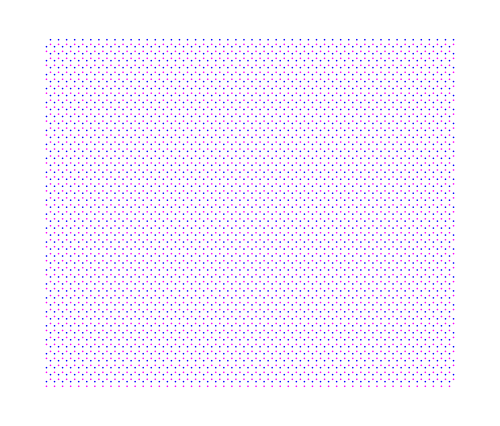

```mathematica
Graphics[Block[{unitVectA={Cos[120 Degree],Sin[120 Degree]},unitVectB={1,0}},Table[unitCell@@(unitVectA j+unitVectB k),{j,1,50},{k,Floor[j/2],50+Floor[j/2]}]],ImageSize->500]
```

```mathematica
Graphics[unitCellK[0,0],ImageSize->100]
```

-Graphics-

```mathematica
L=1;
Graphics[Line[{{L,0},{L/2,L Sqrt[3]/2},{-L/2,L Sqrt[3]/2},{-L,0},{-L/2,-L Sqrt[3]/2},{L/2,-L Sqrt[3]/2},{L,0}}],ImageSize->20]
```

-Graphics-